# Practical 2 (Regula-Falsi)

## Q1. Find approximate root of Cos(x) in the interval (0,2) in 10 iterations. Solution:

```mathematica
f[x_]:=Cos[x]
Subscript[x, 0]=0;
Subscript[x, 1]=2;
e= 0.000001;
iterations=10;
If[f[Subscript[x, 0]]*f[Subscript[x, 1]]>0,Print["These values do not satisfy the IVP so change the initial value."], 
For[n=2,n≤iterations,n++,
Subscript[x, n] = N [  (Subscript[x, n-2]*f[Subscript[x, n-1]]-Subscript[x, n-1]*f[Subscript[x, n-2]])/(f[Subscript[x, n-1]]-f[Subscript[x, n-2]])];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<e ,Return[Subscript[x, n]]];
Print[n-1,"th iteration is: ",Subscript[x, n]]; 
Print ["Estimated error: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]]];
Print["Approximate Root ", Subscript[x, n]]
```

1th iteration is: 1.41228

Estimated error: 0.587717

2th iteration is: 1.57391

Estimated error: 0.161623

3th iteration is: 1.57078

Estimated error: 0.0031228

4th iteration is: 1.5708

Estimated error: 0.0000128049

Return[1.5708]

Approximate Root 1.5708

## Q2. Find approximate root of following equations using the secant method: i) x^3-3 x^2+2x+5=0 ii) Cos(x) - xe^x=0 iii)e^-x=x Solution: i)x^3-3 x^2+2x+5=0

1th iteration is: -0.833333

Estimated error: 0.833333

2th iteration is: -0.962567

Estimated error: 0.129234

3th iteration is: -0.901757

Estimated error: 0.0608094

4th iteration is: -0.904081

Estimated error: 0.00232406

5th iteration is: -0.904161

Estimated error: 0.0000794928

Return[-0.904161]

Approximate Root -0.904161

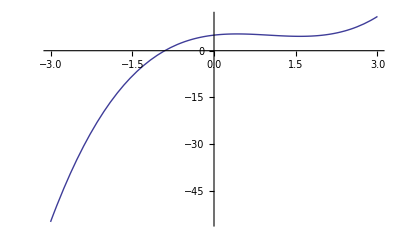

```mathematica
f[x_]:=x^3 -3  x^2+ 2 x + 5 
Subscript[x, 0]=-1;
Subscript[x, 1]=0;
e= 0.000001;
iterations=10;
If[f[Subscript[x, 0]]*f[Subscript[x, 1]]>0,Print["These values do not satisfy the IVP so change the initial value."], 
For[n=2,n≤iterations,n++,
Subscript[x, n] = N [  (Subscript[x, n-2]*f[Subscript[x, n-1]]-Subscript[x, n-1]*f[Subscript[x, n-2]])/(f[Subscript[x, n-1]]-f[Subscript[x, n-2]])];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<e ,Return[Subscript[x, n]]];
Print[n-1,"th iteration is: ",Subscript[x, n]]; 
Print ["Estimated error: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]]];
Print["Approximate Root ", Subscript[x, n]]
Plot[f[x],{x,-3,3}]
```

## ii) Cos(x) - xe^x=0

1th iteration is: -1.86193

Estimated error: 0.861932

2th iteration is: -1.86407

Estimated error: 0.00214255

3th iteration is: -1.864

Estimated error: 0.0000795107

Return[-1.864]

Approximate Root -1.864

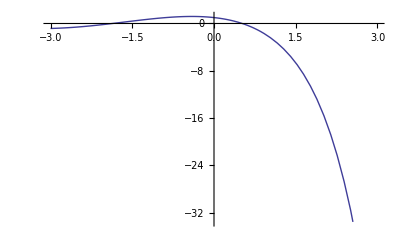

```mathematica
f[x_]:=Cos[x]-x ⅇ^x
Subscript[x, 0]=-2;
Subscript[x, 1]=-1;
e= 0.000001;
iterations=10;
If[f[Subscript[x, 0]]*f[Subscript[x, 1]]>0,Print["These values do not satisfy the IVP so change the initial value."], 
For[n=2,n≤iterations,n++,
Subscript[x, n] = N [  (Subscript[x, n-2]*f[Subscript[x, n-1]]-Subscript[x, n-1]*f[Subscript[x, n-2]])/(f[Subscript[x, n-1]]-f[Subscript[x, n-2]])];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<e ,Return[Subscript[x, n]]];
Print[n-1,"th iteration is: ",Subscript[x, n]]; 
Print ["Estimated error: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]]];
Print["Approximate Root ", Subscript[x, n]]
Plot[f[x],{x,-3,3}]
```

## iii)e^-x=x

1th iteration is: 0.6127

Estimated error: 0.3873

2th iteration is: 0.563838

Estimated error: 0.0488614

3th iteration is: 0.56717

Estimated error: 0.00333197

4th iteration is: 0.567143

Estimated error: 0.0000270518

Return[0.567143]

Approximate Root 0.567143

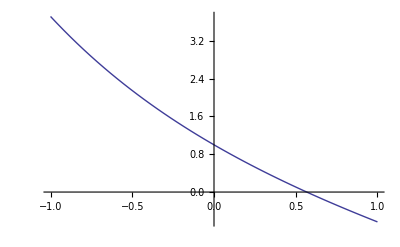

```mathematica
f[x_]:= ⅇ^-x-x
Subscript[x, 0]=0;
Subscript[x, 1]=1;
e= 0.000001;
iterations=10;
If[f[Subscript[x, 0]]*f[Subscript[x, 1]]>0,Print["These values do not satisfy the IVP so change the initial value."], 
For[n=2,n≤iterations,n++,
Subscript[x, n] = N [  (Subscript[x, n-2]*f[Subscript[x, n-1]]-Subscript[x, n-1]*f[Subscript[x, n-2]])/(f[Subscript[x, n-1]]-f[Subscript[x, n-2]])];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<e ,Return[Subscript[x, n]]];
Print[n-1,"th iteration is: ",Subscript[x, n]]; 
Print ["Estimated error: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]]];
Print["Approximate Root ", Subscript[x, n]]
Plot[f[x],{x,-1,1}]
```